```mathematica
D[(1-pf^r)^Np pf^(r N),pf]
```

-Np pf^(-1+r+N r) (1-pf^r)^(-1+Np) r+N pf^(-1+N r) (1-pf^r)^Np r

```mathematica
Simplify[D[(1-p^(p^s r))^Np p^(p^s r (N-s)),p]==0]
```

p^(-1+p^s r (N-s)+s) (1-p^(p^s r))^(-1+Np) r (Np p^(p^s r)+N (-1+p^(p^s r))+s-p^(p^s r) s) (1+s Log[p])==0

```mathematica
D[(1-p^(p^s r))^Np p^(p^s r (N-s)),s]
```

-Np p^(p^s r+p^s r (N-s)+s) (1-p^(p^s r))^(-1+Np) r Log[p]^2+p^(p^s r (N-s)) (1-p^(p^s r))^Np Log[p] (-p^s r+p^s r (N-s) Log[p])

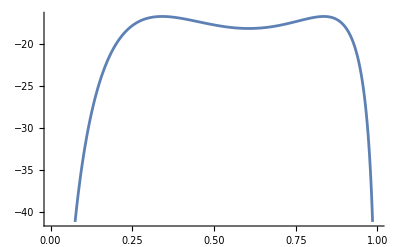

```mathematica
Plot[Np Log[(1-q^(q^s r))]+q^s r (N-s)Log[q]/.{N->10,Np->20,r->10,s->2},{q,0,1}]
```

```mathematica
Manipulate[Plot[(1-q^(q^s r))^Np q^(q^s r (N-s))/.{N->10,Np->20,r->20},{q,0,1},PlotRange->{0,8*10^-6}],{s,0,10}]
```

General::munfl: 0.0000204286^200. is too small to represent as a normalized machine number; precision may be lost.

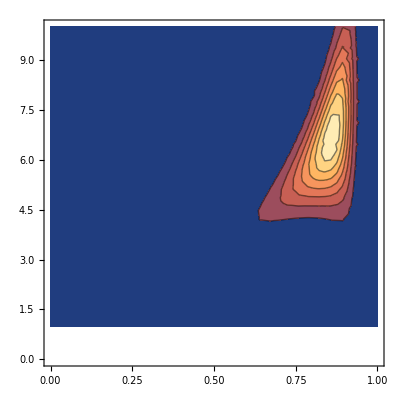

```mathematica
ContourPlot[(1-q^(q^s r))^Np q^(q^s r (N-s))/.{N->10,Np->20,r->20},{q,0,1},{s,1,10},PlotRange->{0,8*10^-6}]
```

```mathematica
Simplify[D[(1-q^(q^s r))^Np q^(q^s r (N-s)),q]==0]
```

q^(-1+q^s r (N-s)+s) (1-q^(q^s r))^(-1+Np) r (Np q^(q^s r)+N (-1+q^(q^s r))+s-q^(q^s r) s) (1+s Log[q])==0

```mathematica
Simplify[D[(1-q^(q^s r))^Np q^(q^s r (N-s)),s]==0]
```

q^(q^s r (N-s)+s) (1-q^(q^s r))^(-1+Np) r Log[q] (-1+q^(q^s r)-(Np q^(q^s r)+N (-1+q^(q^s r))+s-q^(q^s r) s) Log[q])==0

```mathematica
N[E/r Log[1+Np/N]/.{N->10,Np->20,r->20}]
```

0.149317